# Laplace T1 Setup

```mathematica
<<AceGen`;
SMSInitialize["T1_Laplace","Environment"->"AceFEM","Mode"->"Optimal"];
SMSTemplate[
"SMSTopology"->"T1",
"SMSNoNodes"->3,
"SMSDOFGlobal"->{1,1,1},
"SMSDefaultIntegrationCode"->41,
"SMSNodeID"->{"T","T","T"},
"SMSDomainDataNames" -> {"k"},
"SMSDefaultData"-> {1},
"SMSSymmetricTangent"->False
];

SMSStandardModule["Tangent and residual"]
k⊢SMSReal[es$$["Data",1]];
XI⊢Table[SMSReal[nd$$[i,"X",j]],{i,SMSNoNodes},{j,SMSNoDimensions}];
UI⊢Table[SMSReal[nd$$[i,"at",j]],{i,SMSNoNodes},{j,SMSDOFGlobal⟦i⟧}];
DOFVector⊨Flatten[UI];
SMSDo[Ig,1,SMSInteger[es$$["id","NoIntPoints"]]];
Ξ={ξ,η,ζ}⊢Table[SMSReal[es$$["IntPoints",i,Ig]],{i,3}];
ω⊢SMSReal[es$$["IntPoints",4,Ig]];
SHP⊨{ξ,η,1-ξ-η};
SMSFreeze[X,Append[SHP.XI⟦1;;3⟧,ζ]];
Jm⊨SMSD[X,Ξ];
detJ⊨SMSDet[Jm];
θ⊨SHP.Flatten[UI];
Gradθ⊨SMSD[θ,X,"Dependency"->{Ξ,X,SMSInverse[Jm]}];
SMSFreeze[q,-Gradθ k];
Π⊨q.Gradθ;
δΠ⊨SMSD[Π detJ ω,DOFVector,"Constant"->{q}];
ΔδΠ⊨SMSD[δΠ,DOFVector];
SMSExport[ΔδΠ,s$$,"AddIn"->True];
SMSExport[δΠ,p$$,"AddIn"->True];
SMSEndDo[];

SMSStandardModule["Postprocessing"];
SMSGPostNames={"T"};
k⊢SMSReal[es$$["Data",1]];
XI⊢Table[SMSReal[nd$$[i,"X",j]],{i,SMSNoNodes},{j,SMSNoDimensions}];
UI⊢Table[SMSReal[nd$$[i,"at",j]],{i,SMSNoNodes},{j,SMSDOFGlobal⟦i⟧}];
DOFVector⊨Flatten[UI];
SMSDo[Ig,1,SMSInteger[es$$["id","NoIntPoints"]]];
Ξ={ξ,η,ζ}⊢Table[SMSReal[es$$["IntPoints",i,Ig]],{i,3}];
ω⊢SMSReal[es$$["IntPoints",4,Ig]];
SHP⊨{ξ,η,1-ξ-η};
SMSFreeze[X,Append[SHP.XI⟦1;;3⟧,ζ]];
Jm⊨SMSD[X,Ξ];
detJ⊨SMSDet[Jm];
θ⊨SHP.Flatten[UI];
SMSExport[Flatten[{θ}],gpost$$[Ig,#1]&];
SMSEndDo[];

SMSWrite[];
```

Unknown options.
 Description:     Option "LocalAuxiliaryVariables" passed to a function {SMSInitialize} is not one of the known options for that function. Known options for a function{SMSInitialize}are:{"GlobalNames", "VectorLength", "SubroutineName", "NumberOfExamples", "Language", "Debug", "Mode", "CollectInput", "StartingBreakPoint", "Environment", "Precision", "PrintOptions", "Parallel"}
Events: 0
Version: 7.204 MacOSX (8 Dec 20) (MMA 12.2) Module: SMSInitialize
See also:   AceGen Troubleshooting  Continue

$Aborted

$Aborted

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{{SKR,{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{},{}},{},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{{True,True},{True,True},«4»,{True,True},{True,True}},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{True,True,True,True,True,True,True,True},{ElementSpec *es,ElementData *ed,NodeSpec **ns,NodeData **nd,double *rdata,int *idata,double *p,double **s},{3,3,3,3,3,3,3,3},«8»},«5»,{«1»}},{«1»}}⟦0,1,7⟧ is longer than depth of object.

4.60879

2.05528×10^-15

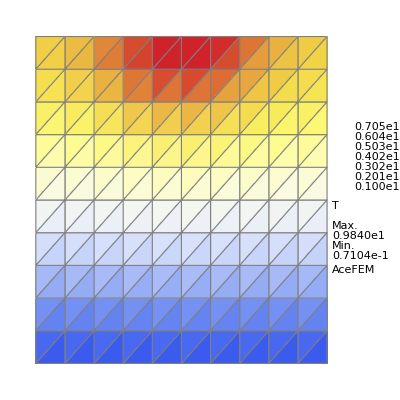

```mathematica
<<AceFEM`;
SMTInputData[];
SMTAddDomain[{"Ω","T1_Laplace",{}}];
L=20;
SMTAddMesh[Polygon[{{0,0},{10,0},{10,10},{0,10}}],"Ω","T1",{10,10}];
SMTAddEssentialBoundary["Y"==0&&"ID"=="T"&,1->0];
SMTAddEssentialBoundary[Line[{{4,10},{6,10}},"T"],1->10];
SMTAnalysis[];
SMTNextStep[1,1];
SMTNewtonIteration[]
SMTNewtonIteration[]
SMTShowMesh["Field"->"T"]
```